# School of Business and Economics Maastricht University

## Dynamic Modelling & Dynamic Optimisation, March 2023

## Marek Chadim . Oscar Monville

## Final case

## Setup

```mathematica
Max∫_0^∞ p*c[t]-f[c[t]]*e^δt ⅆt
```

s.t. ṡ(t)=g(s[t])-c[t]
           s(0)=s_0
with 
s(t)→ quantity of fish in the lake at time t
c(t)→ the rate of fish being caught at time t

g(s)→ the growth rate of the amount of fish
		g(0)=0, g'(s)>0 for s<s*, g'(s)<0 for s>s*, thus g''(s)<0
f(c)→ cost of fish being caught
		f'(c)>0, f''(c)>0,

δ > 0 →  discount factor
s0 > 0 → initial amount of fish in the lake.
p > 0 → fixed positive price of fish

Discuss the stability of the equilibria and draw potential optimal trajectories in each of the phase diagrams . 
Explain your results .

## Specification

Let us first consider functions and constants satisfying the given criteria

```mathematica
ClearAll["Global`*"]
g[s[t]]:=s[t]-s[t]^2/100;
sstar= Solve[ D[g[s[t]],s[t]]==0, s[t]][[1,1,2]];
check1={D[g[s[t]],s[t]]/.s[t]->sstar-1 ,D[g[s[t]],s[t]]/.s[t]->sstar+1,D[D[g[s[t]],s[t]],s[t]]<0};
f[c[t]]:=c[t]^2;
check2={D[f[c[t]],c[t]],D[D[f[c[t]],c[t]],c[t]]>0};
 := 1;
p := 10;
s0:= 50;
```

## Maximum principle

Since the problem is autonomous, we can form the current - value Hamiltonian and obtain the necessary conditions

```mathematica
Hamiltonian:H=(p*c[t]-f[c[t]])+ψ[t](g[s[t]]-c[t])
```

10 c[t]-c[t]^2+(-c[t]+s[t]-s[t]^2/100) ψ[t]

```mathematica
C1=D[H,c[t]]==0
C2=D[H,ψ[t]]==s'[t]
C3=D[H,s[t]]== ψ[t]-ψ'[t]
```

10-2 c[t]-ψ[t]==0

-c[t]+s[t]-s[t]^2/100==s'[t]

(1-s[t]/50) ψ[t]==0

## (s, c) - space

### Solving

Expressing ψ[t] and  in terms of s[t] and c[t]

```mathematica
ψ'[t]=Solve[C3,{ψ'[t]},{t}][[1,1,2]]
```

Solve::ivar: ψ[t] (1-g'[s[t]]) is not a valid variable.

ψ[t]

```mathematica
ψ[t]=Solve[C1,{ψ[t]},{t}][[1,1,2]]
```

-2 (-5+c[t])

Differentiating with respect to obtain equation for c'[t]

```mathematica
D[C1,t]
```

-ψ[t]-2 c'[t]==0

Defining the system of differential equations and obtaining a numerical approximation

```mathematica
sys1={s'[t]==+s[t]-s[t]^2/100-c[t],c'[t]==1/50 (-5+c[t]) s[t], s[0]==s0,c[0]==c0};
DSolve[sys1,{s,c}, t]
sysol1:= NDSolve[sys1,{s,c},{t,-5,5}];
```

Solve::naqs: C3 is not a quantified system of equations and inequalities.

Part::partd: Part specification Solve[C3,{ψ'[t]},{t}]⟦1,1,2⟧ is longer than depth of object.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

Solve::naqs: C3 is not a quantified system of equations and inequalities.

Part::partd: Part specification Solve[C3,{TerminatedEvaluation[RecursionLimit]},{t}]⟦1,1,2⟧ is longer than depth of object.

Solve::ivar: 1/50 s[t] ψ[t] is not a valid variable.

1/50 s[t] ψ[t]

1/50 s[t] ψ[t]

-2 (-5+c[t])

-ψ[t]-2 c'[t]==0

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

DSolve[{s'[t]==-c[t]+s[t]-s[t]^2/100,c'[t]==1/50 (-5+c[t]) s[t],s[0]==50,c[0]==0},{s,c},t]

NDSolve::ndsz: At t == 3.02579, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[…]

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

TerminatedEvaluation[RecursionLimit]

### Plotting

Solution functions (s[t],c[t] ) with  various initial conditions displayed  in the (s,c) plane:

```mathematica
phase1= 
Show[
Table[
ParametricPlot[
Evaluate[{s[t],c[t]}/.sysol1],
{t,-5,5},
PlotStyle->RGBColor[1,0,0]],
{s0,-50,100,50},{c0,-50,100,50}],
PlotRange->{{-5,150},{-50,100}},AxesLabel->{"s","c"},PlotLabel->"Phase diagram"]
```

NDSolve::ndsz: At t == 1.62071, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 3.02579, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 2.34074, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-4.9998} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-4.9998} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 2.34074, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 3.02579, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 1.62071, step size is effectively zero; singularity or stiff system suspected.

Expressions for s’[t] and c’[t] in terms of s and c at each point (s,c) give the direction of the tangent line at this point to the particular solution of the system passing through that point:

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
sc
```

{s'[t]==-c[t]+s[t]-s[t]^2/100,c'[t]==1/50 (-5+c[t]) s[t],s[0]==50,c[0]==c0}

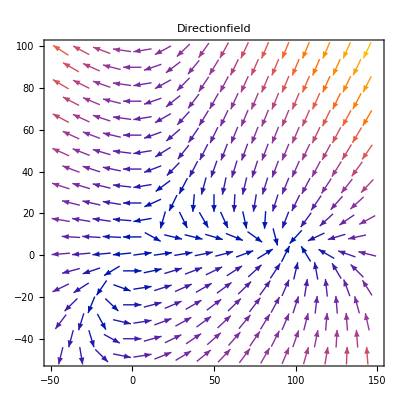

```mathematica
dirplot1 =VectorPlot[{-c+s-s^2/100,-1/50 (-5+c) s},{s,-50,150},{c,-50,100},PlotLabel->"Directionfield"]
```

Finally, adding the curves s'=0 and c'=0 allows for  visualizing the intersection-point of these curves, i.e. the equilibrium-points of the system.

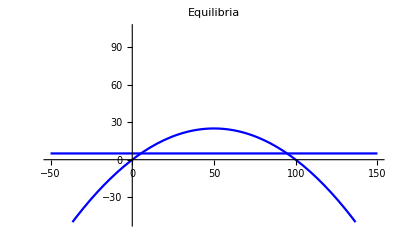

```mathematica
zeroprimeplot1=Plot[{s-s^2/100,5},{s,-50,150},
PlotStyle->RGBColor[0,0,1],
PlotRange->{-50,105},PlotLabel->"Equilibria"]
```

```mathematica
sceq=Solve[{s-s^2/100-c==0,1/50 (-5+c) s==0},{s,c}]
```

{{s→0,c→0},{s→10 (5-2 √5),c→5},{s→10 (5+2 √5),c→5}}

```mathematica
sceq1=First[sceq]
```

{s→0,c→0}

```mathematica
sceq2=sceq[[2,{1,2}]]
```

{s→10 (5-2 √5),c→5}

```mathematica
sceq3= Last[sceq]
```

{s→10 (5+2 √5),c→5}

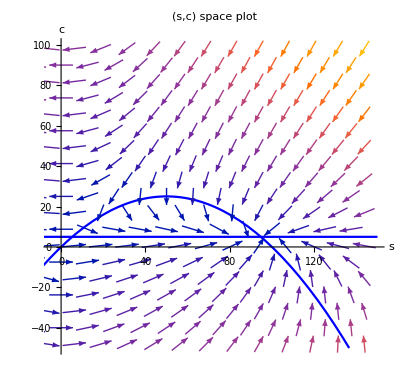

```mathematica
Show[phase1,dirplot1,zeroprimeplot1, PlotLabel->"(s,c) space plot"]
```

#### Analysing stability

Write text here

```mathematica
sc
```

{s'[t]==-c[t]+s[t]-s[t]^2/100,c'[t]==1/50 (-5+c[t]) s[t],s[0]==50,c[0]==c0}

```mathematica
sdot:= s[t]-s[t]^2/100-c[t]
```

```mathematica
cdot:=1/50 (-5+c[t]) s[t]

A={{D[sdot,s[t]],D[sdot,c[t]]},{D[cdot,s[t]],D[cdot,c[t]]}}
```

{{1-s[t]/50,-1},{1/50 (-5+c[t]),s[t]/50}}

```mathematica
MatrixForm[A]
```

(1-s[t]/50 | -1
1/50 (-5+c[t]) | s[t]/50)

```mathematica
Det[A]/.{s[t]->0,c[t]->0}
```

-1/10

10 (5-2 √5)

```mathematica
N[Eigenvalues[A]/.{s[t]->0,c[t]->0}]
```

```mathematica
{-0.09160797830996159,1.0916079783099617}
```

{-0.091608,1.09161}

10 (5-2 √5)

```mathematica
s2= sceq2[[1,2]]
```

10 (5-2 √5)

```mathematica
Det[A]/.{s[t]->s2,c[t]->5}
```

1/5 (5-2 √5)-1/25 (5-2 √5)^2

```mathematica
N[1/5 (5-2 √5)-1/25 (5-2 √5)^2]
```

0.0944272

```mathematica
N[Eigenvalues[A]/.{s[t]->s2,c[t]->5}]
```

{0.105573,0.894427}

```mathematica
s3= sceq3[[1,2]]
```

10 (5+2 √5)

```mathematica
Det[A]/.{s[t]->s3,c[t]->5}
```

1/5 (5+2 √5)-1/25 (5+2 √5)^2

```mathematica
N[1/5 (5+2 √5)-1/25 (5+2 √5)^2]
```

-1.69443

```mathematica
N[Eigenvalues[A]/.{s[t]->0,c[t]->0}]
```

{-0.091608,1.09161}

## (s,)-space

s[t]/50

```mathematica
1/50 s[t] ψ[t]
```

1/50 s[t] ψ[t]

```mathematica
C2
```

-c[t]+s[t]-s[t]^2/100==s'[t]

```mathematica
Solve[C2,s'[t],t]/. c[t]->5-ψ[t]/2
```

Solve::bdomv: Warning: t is not a valid domain specification. Assuming it is a variable to eliminate.

{{s'[t]→1/100 (100 s[t]-s[t]^2-100 (5-ψ[t]/2))}}

```mathematica
sys1={s'[t]==+s[t]-s[t]^2/100-c[t],c'[t]==1/50 (-5+c[t]) s[t], s[0]==s0,c[0]==c0}

ClearAll["Global`*"]
```

{s'[t]==-c[t]+s[t]-s[t]^2/100,c'[t]==1/50 (-5+c[t]) s[t],s[0]==s0,c[0]==c0}

```mathematica
sys2= {s'[t]==1/100 (100 s[t]-s[t]^2-100 (5-ψ[t]/2)),ψ'[t]==1/50 s[t] ψ[t], s[0]==s0,ψ[0]==ψ0}
```

{s'[t]==1/100 (100 s[t]-s[t]^2-100 (5-ψ[t]/2)),True,s[0]==s0,ψ[0]==ψ0}

```mathematica
DSolve[sys2,{s[t],ψ[t]},{t}]
```

DSolve::deqn: Equation or list of equations expected instead of True in the first argument {s'[t]==1/100 (100 s[t]-s[t]^2-100 (5-1/2 ψ[«1»])),True,s[0]==s0,ψ[0]==ψ0}.

DSolve[{s'[t]==1/100 (100 s[t]-s[t]^2-100 (5-ψ[t]/2)),True,s[0]==s0,ψ[0]==ψ0},{s[t],ψ[t]},{t}]

```mathematica
sysol2:=NDSolve[sys2,{s,ψ},{t,-10,10}];
```

```mathematica
phase2= 
Show[
Table[
ParametricPlot[
Evaluate[{s[t],ψ[t]}/.sysol2],
{t,-10,10},
PlotStyle->RGBColor[1,0,0]],
{s0,-50,100,50},{ψ0,-50,50, 50}],
PlotRange->{{-50,150},{-50,100}},AxesLabel->{"s","ψ"}, PlotLabel->"Insert Title Here"]
```

ReplaceAll::reps: {sysol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

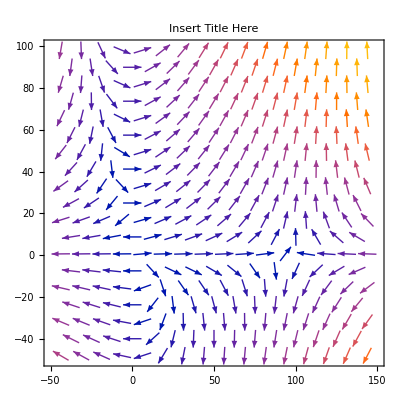

```mathematica
dirplot2 =VectorPlot[{s-s^2/100 -5+ψ/2,ψ/50  s},{s,-50,150},{ψ,-50,100}, PlotLabel->"Insert Title Here"]
```

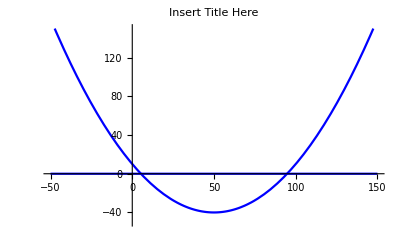

```mathematica
zeroprimeplot2=Plot[{s^2/50-2s+10,0},{s,-50,150},
PlotStyle->RGBColor[0,0,1],
PlotRange->{-50,150}, PlotLabel->"Insert Title Here"]
```

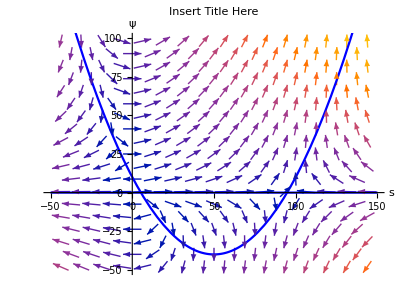

```mathematica
Show[phase2,dirplot2,zeroprimeplot2, PlotLabel->"Insert Title Here"]
```

```mathematica
sys2
```

{s'[t]==1/100 (100 s[t]-s[t]^2-100 (5-ψ[t]/2)),True,s[0]==s0,ψ[0]==ψ0}

```mathematica
sdot:= s[t]-s[t]^2/100 -5+ψ[t]/2
```

```mathematica
psidot:= 1/50 s[t] ψ[t]
```

```mathematica
B={{D[sdot,s[t]],D[sdot,ψ[t]]},{D[psidot,s[t]],D[psidot,ψ[t]]}}
```

{{1-s[t]/50,1/2},{ψ[t]/50,s[t]/50}}

```mathematica
MatrixForm[B]
```

(1-s[t]/50 | 1/2
ψ[t]/50 | s[t]/50)

```mathematica
({{1-s[t]/50, 1/2}, {ψ[t]/50, s[t]/50}})
```

{{1-s[t]/50,1/2},{ψ[t]/50,s[t]/50}}

```mathematica
Det[B]/.{s[t]->0,ψ[t]->10}
```

-1/10

```mathematica
N[Eigenvalues[B]/.{s[t]->0,ψ[t]->10}]
```

{-0.091608,1.09161}

```mathematica
Det[B]/.{s[t]->s1,ψ[t]->0}
```

s1/50-s1^2/2500

```mathematica
N[1/5 (5-2 √5)-1/25 (5-2 √5)^2]
```

0.0944272

```mathematica
N[Eigenvalues[B]/.{s[t]->s1,ψ[t]->0}]
```

{0.02 (25.-1. √(625.-50. s1+s1^2)),0.02 (25.+√(625.-50. s1+s1^2))}

```mathematica
Det[B]/.{s[t]->s2,ψ[t]->0}
```

s2/50-s2^2/2500

```mathematica
N[1/5 (5+2 √5)-1/25 (5+2 √5)^2]
```

-1.69443

```mathematica
N[Eigenvalues[B]/.{s[t]->s2,ψ[t]->0}]
```

{0.02 (25.-1. √(625.-50. s2+s2^2)),0.02 (25.+√(625.-50. s2+s2^2))}